```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

## n \mapsto t[n] is defined as a table in myFunctionsPureCodeV8 copy.nb, whhich is loaded by myFunctionsMathematica8.m. The table was created in my2ndEditOdlyzkoAccrtZrs6dec15.nb. It is from a table on Odlyzko’s site.

```mathematica
strm=OpenRead["2000 better zeros copy 2"];
zrs=ReadList[strm];
zero[n_]:=zrs[[n]]
```

```mathematica
Length[zrs]
```

5051

```mathematica
bestzero[5000]
```

1/2+ⅈ t[5000]

```mathematica
Max[errors]
```

2.×10^-1996

seconds 215.45727

seconds 418.85969

seconds 603.09434

seconds 768.53021

seconds 933.548792

seconds 1098.31313

seconds 1244.77266

seconds 1392.41483

seconds 1539.60023

seconds 1686.42593

seconds 1832.66924

seconds 1978.54174

seconds 2135.81688

seconds 2262.39284

seconds 2389.28623

seconds 2519.08123

seconds 2643.75811

seconds 2767.25259

seconds 2890.35917

seconds 3013.11931

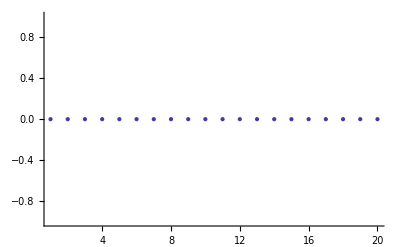

realfxptsprecision1000no1

```mathematica
stream=OpenWrite["realfxptsprecision1000no1"];
precision=1000;
errors={};
start=SessionTime[];
For[n=0,n<20,n++;
startcenter=-18-2*n;
fx=FindRoot[Zeta[u]-u,{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
Write[stream,{n,fx}];
Print["seconds ",SessionTime[]-start];
error=Abs[Zeta[fx]-fx];
errors=Append[errors,error]];
Print[ListPlot[errors]];
Close[stream]
```

```mathematica
stream=OpenAppend["realfxptsprecision1000no1"];
precision=1000;
errors={};
start=SessionTime[];
For[n=20,n<30,n++;
startcenter=-18-2*n;
fx=FindRoot[Zeta[u]-u,{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
Write[stream,{n,fx}];
error=Abs[Zeta[fx]-fx];
errors=Append[errors,error]];
Print[ListPlot[errors]];
Print["seconds ",SessionTime[]-start];
Close[stream]
-
```

$Aborted

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{}]

seconds 100.67491

realfxptsprecision1000no1

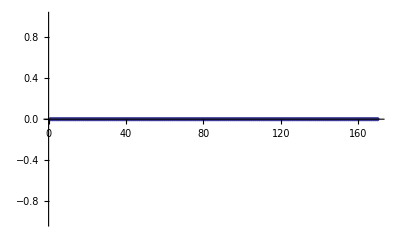

seconds 9626.347909

realfxptsprecision1000no1

```mathematica
stream=OpenAppend["realfxptsprecision1000no1"];
precision=1000;
errors={};
start=SessionTime[];
For[n=30,n<200,n++;
startcenter=-18-2*n;
fx=FindRoot[Zeta[u]-u,{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
Write[stream,{n,fx}];
error=Abs[Zeta[fx]-fx];
errors=Append[errors,error]];
Print[ListPlot[errors]];
Print["seconds ",SessionTime[]-start];
Close[stream]
```